```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

Load pre-processed data

```mathematica
Get[NotebookDirectory[]<>"../../Data/WT/mesh-data.mx"]
```

### Define tissue regions (ventral germ band, lateral germ band, dorsal pole)

```mathematica
dvAngle[p_]:=-π+0.1+toCylinder[p][[2]]/$radius
```

```mathematica
dvStratifiedBodyCells=Join[
Table[
Select[bodyCells,ϕ<Abs[dvAngle[cellCentroidsTS[[1]][#]]]<ϕ+0.1π&],
{ϕ,0.2π,π-0.2π,0.1π}
],
{Select[bodyCells,π-0.1π<Abs[dvAngle[cellCentroidsTS[[1]][#]]]&]}
];
```

```mathematica
zoneColors=RGBColor@@(#/255)&/@{{100,100,250},{102,194,165},{252,141,98}}
```

{RGBColor[Rational[20, 51], Rational[20, 51], Rational[50, 51]],RGBColor[Rational[2, 5], Rational[194, 255], Rational[11, 17]],RGBColor[Rational[84, 85], Rational[47, 85], Rational[98, 255]]}

```mathematica
zoneColorsLight=Blend[{White,#},0.2]&/@zoneColors
```

{RGBColor[0.8784313725490196, 0.8784313725490196, 0.996078431372549],RGBColor[0.88, 0.952156862745098, 0.9294117647058824],RGBColor[0.9976470588235294, 0.9105882352941177, 0.8768627450980392]}

```mathematica
zoneCells={
dvStratifiedBodyCells[[1]],
Catenate[dvStratifiedBodyCells[[2;;5]]],
Catenate[dvStratifiedBodyCells[[7;;8]]]
};
```

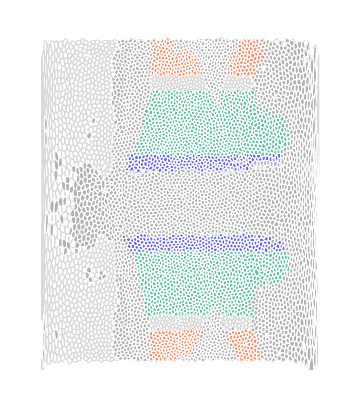

```mathematica
Graphics[{
EdgeForm[LightGray],FaceForm[None],
renderCell2D[#,1]&/@Complement[Keys[cellCentroidsTS[[1]]],invaginatingCells],
EdgeForm[White],FaceForm[GrayLevel[0.7]],
renderCell2D[#,1]&/@invaginatingCells,
Table[{
FaceForm[zoneColors[[i]]],
renderCell2D[#,1]&/@zoneCells[[i]]
},
{i,Length[zoneCells]}
]},
PlotRange->{{0,520},{-10,560}}
]
```

### Tension-isogonal decomposition at individual vertices (Fig. 6)

#### Setup

We need to exclude extremely elongated (i.e. nearly degenerate) triangles from this analysis. The average tension for each triangle is normalized to 1 (i.e. the perimeter is 3). The triangle area is therefore a measure for the degree of elongation of the triangle.
Let’s plot a cummulative distribution of areas to find a reasonable cutoff

```mathematica
vertexData=With[{t=120},With[{
vertices=First/@Position[Length/@vertexCellsTS[[t]],3]
},
DeleteCases[
{#,vertexTensionTriangle[#,t]}&/@vertices,
{_,_Missing}
]
]
];//AbsoluteTiming
```

{3.3441,Null}

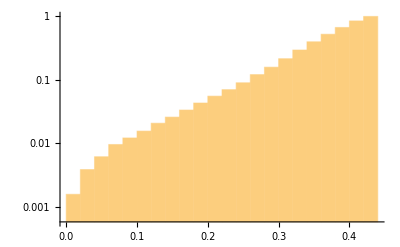

```mathematica
Histogram[triArea[#[[3]]-#[[1]],#[[2]]-#[[1]]]&/@vertexData[[All,2]],Automatic,"CDF",PlotRange->All,ScalingFunctions->"Log"]
```

At a threshold of about 0.15, we cut off about 2% of the most elongated triangles. The “threshold” triangle with area 0.15 is illustrated below

```mathematica
abortOnMessageOn[]
```

```mathematica
Off[triArea::neg]
```

```mathematica
vertexIsogonalDeformation[v_Integer,t_Integer,scaleFactor_?NumberQ]:=Module[{
triplet=vertexCellsTS[[t,v]],
coords,
tCoords,A,
areaThresh=0.15,lengthThresh=0.5
},
If[Length[triplet]!=3,
Return[Missing["DegenerateVertex",{v,t}]]
];
coords=getTripletCoords[triplet,t];
If[Min[Norm/@coords[[2]]]<lengthThresh,
Return[Missing["ShortEdge",{v,t}]]
];
tCoords=tensionTriangle[Normalize/@coords[[2]]];

If[MissingQ[tCoords],Return[tCoords]];

A=Abs[triArea[tCoords[[2]]-tCoords[[1]],tCoords[[3]]-tCoords[[1]]]];
(* Very small areas indicate degenerate triangles and will be discarded (the tensions are initially normalized to average to 1) *)
If[A<areaThresh,Return[Missing["SmallArea",{v,t}]]];
tCoords=tCoords/√A;
fitDeformationMatrix2D[scaleFactor tCoords,coords[[1]],"Symmetric"][[3]]
]
```

#### Calibrate scale factor

```mathematica
Off[triArea::neg]
```

TP 2

```mathematica
scaleFactorSweep=With[{t=1},
Table[
With[{
vertices=Select[Union[Catenate[cellVerticesTS[[t]]/@bodyCells]],Length[vertexCellsTS[[t,#]]]==3&]
},
{scaleFactor,DeleteMissing[vertexIsogonalDeformation[#,t,scaleFactor]&/@vertices]}
],
{scaleFactor,3,6,0.25}
]
];//AbsoluteTiming
```

{29.6077,Null}

```mathematica
Length[scaleFactorSweep]
```

13

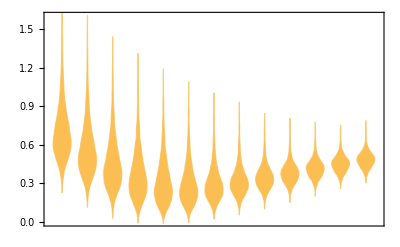

```mathematica
DistributionChart[Norm[#-IdentityMatrix[2],"Frobenius"]&/@#&/@scaleFactorSweep[[All,2]],PlotRange->{0,1.6}]
```

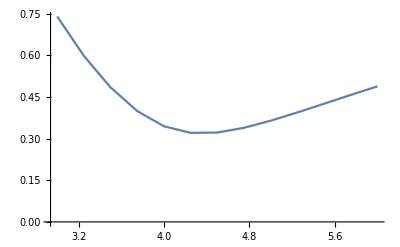

```mathematica
ListLinePlot[{#[[1]],Mean[Norm[#-IdentityMatrix[2],"Frobenius"]&/@#[[2]]]}&/@scaleFactorSweep]
```

Mean norm (Frobenius) of the isogonal strain tensor as a function of the scale factor η. 

We can also estimate the scale factor from the fact that tensions are initially nearly isotropic, i.e. the tension triangles are on average equilateral. Since we normalize the tension triangle area to 1, the tension triangle edge length is √(4/√3). The scale factor η has to convert this into the average cell centoid distance 6.4 µm, which yields a scale factor of about 4.2, in good agreement with the minimum norm found in the above sweep.

```mathematica
4.2 2./√(√3)
```

6.38262

```mathematica
Mean[Catenate[With[{c=cellCentroidsTS[[1]][#]},Norm[c-cellCentroidsTS[[1]][#]]&/@cellNeighborsTS[[1]][#]]&/@bodyCells]]
```

6.37128

#### Tissue patch rendering (Fig. 6S1)

Germ band patch (stationary frame)

```mathematica
inFrame[p_,{{x0_,x1_},{y0_,y1_}}]:=x0<p[[1]]<x1&&y0<p[[2]]<y1
```

```mathematica
renderROI[t_]:=Module[{
roi={{220,270},{300,350}},
cells,vertices,tensions,isoF
},
cells=Keys[Select[
cellCentroidsTS[[t]],
inFrame[toCylinder[#],{{-5,5},{-5,5}}+roi]&
]];
vertices=First/@Position[vertexCoordsTS[[t]],_?(inFrame[toCylinder[#],roi]&)];
isoF=vertexIsogonalDeformation[#,t,4.5]&/@vertices;
Graphics[{
FaceForm[GrayLevel[0.9]],EdgeForm[None],
FaceForm[White],
EdgeForm[{Gray,AbsoluteThickness[1]}],
renderCell2D[#,t]&/@cells,
(*AbsolutePointSize[4],Gray,
Point[toCylinder[#]]&/@vertexCoordsTS[[t,vertices]],*)
AbsoluteThickness[3],
MapThread[If[!MissingQ[#2],renderTensor[toCylinder[vertexCoordsTS[[t,#1]]],#2-IdentityMatrix[2],3]]&,{vertices,isoF}]
},
PlotRange->roi,
Background->GrayLevel[1],
ImageSize->200
]
]
```

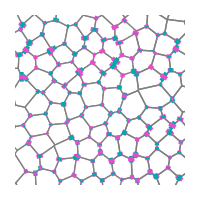
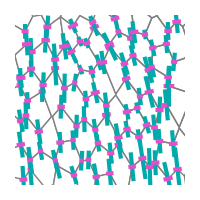
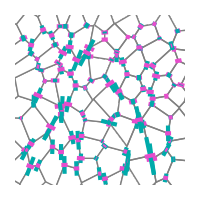
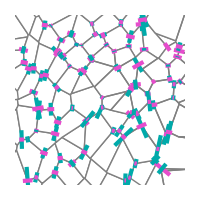

```mathematica
renderROI/@{2,90,150,198}
```

Dorsal patch (stationary frame)

```mathematica
renderROI[t_]:=Module[{
roi={{220,270},{500,550}},
cells,vertices,tensions,isoF
},
cells=Keys[Select[
cellCentroidsTS[[t]],
inFrame[toCylinder[#],{{-5,5},{-5,5}}+roi]&
]];
vertices=First/@Position[vertexCoordsTS[[t]],_?(inFrame[toCylinder[#],roi]&)];
isoF=vertexIsogonalDeformation[#,t,4.5]&/@vertices;
Graphics[{
FaceForm[GrayLevel[0.9]],EdgeForm[None],
FaceForm[White],
EdgeForm[{Gray,AbsoluteThickness[1]}],
renderCell2D[#,t]&/@cells,
(*AbsolutePointSize[4],Gray,
Point[toCylinder[#]]&/@vertexCoordsTS[[t,vertices]],*)
AbsoluteThickness[3],
MapThread[If[!MissingQ[#2],renderTensor[toCylinder[vertexCoordsTS[[t,#1]]],#2-IdentityMatrix[2],3]]&,{vertices,isoF}]
},
PlotRange->roi,
Background->GrayLevel[1],
ImageSize->200
]
]
```

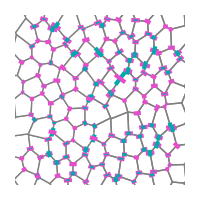
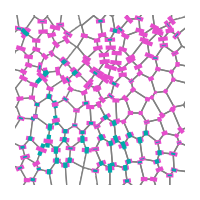
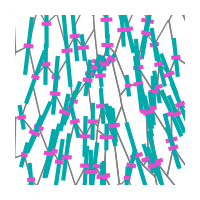
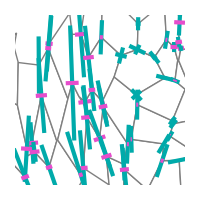

```mathematica
renderROI/@{2,90,150,198}
```

#### Whole embryo rendering (Fig. 6B,B’ and Fig. 6S1)

```mathematica
vertexData=With[{t=2,scaleFactor=4.2},With[{
vertices=First/@Position[Length/@vertexCellsTS[[t]],3]
},
DeleteCases[
{toCylinder[vertexCoordsTS[[t,#]]],vertexIsogonalDeformation[#,t,scaleFactor]}&/@vertices,
{_,_Missing}
]
]
];//AbsoluteTiming
```

{6.1431,Null}

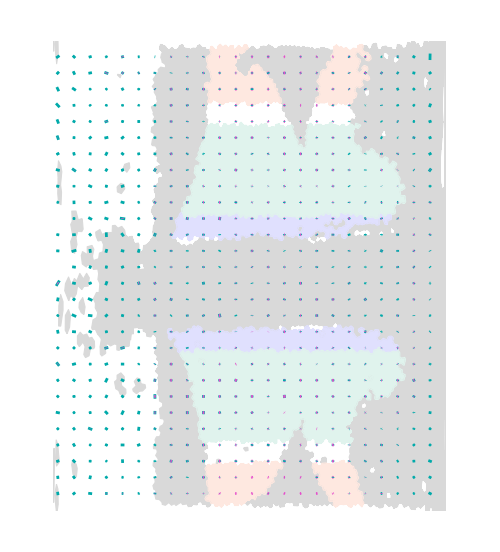

```mathematica
With[{
t=2,
binnedData=Mean[#[[All,2]]]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&]
},Graphics[{
AbsolutePointSize[5],AbsoluteThickness[2],
FaceForm[LightGray],EdgeForm[LightGray],
renderCellGroup2D[invaginatingCells,t],
Table[{
FaceForm[zoneColorsLight[[i]]],EdgeForm[zoneColorsLight[[i]]],,
renderCellGroup2D[zoneCells[[i]],t]
},
{i,Length[zoneCells]}
],
EdgeForm[{Dashed,AbsoluteThickness[1],Black}],FaceForm[None],
KeyValueMap[Function[{c,tensor},
If[c[[1]]<500,
renderTensor[c,tensor-IdentityMatrix[2],5]
]],
binnedData
]},
ImageSize->500,Background->White,
PlotRange->{{5,510},{0,2π $radius}}
]
]
```

TP 150

```mathematica
vertexData=With[{t=150},With[{
vertices=First/@Position[Length/@vertexCellsTS[[t]],3]
},
DeleteCases[
{toCylinder[vertexCoordsTS[[t,#]]],vertexIsogonalDeformation[#,t,6]}&/@vertices,
{_,_Missing}
]
]
];//AbsoluteTiming
```

{4.07259,Null}

```mathematica
binnedData=Mean[#[[All,2]]]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&];
```

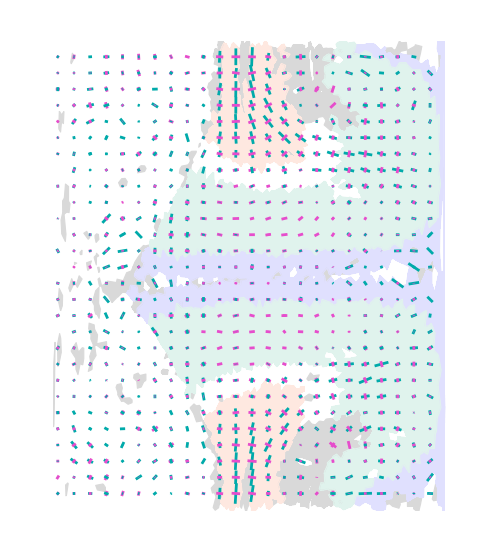

```mathematica
With[{t=150},Graphics[{
AbsolutePointSize[5],AbsoluteThickness[2],
FaceForm[LightGray],EdgeForm[LightGray],
renderCellGroup2D[invaginatingCells,t],
Table[{
FaceForm[zoneColorsLight[[i]]],EdgeForm[zoneColorsLight[[i]]],,
renderCellGroup2D[zoneCells[[i]],t]
},
{i,Length[zoneCells]}
],
KeyValueMap[Function[{c,tensor},
If[c[[1]]<500,
renderTensor[c,tensor-IdentityMatrix[2],8]
]],
binnedData
]},
ImageSize->500,Background->White,
PlotRange->{{5,510},{0,2π $radius}}
]
]
```

#### Average isogonal deformation as a function of time for different tissue regions (Fig. 6C)

Load advected basis vectors precomputed in pre-processing.nb

```mathematica
advectedCellBasisTS=Import[NotebookDirectory[]<>"../../Data/WT/advectedCellBasisTS.mx"];
```

Visualize advected DV basis vector vectors in pulback

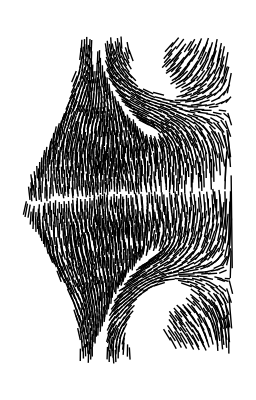

```mathematica
Graphics[{
Line[toCylinder[{#[[2]]-10#[[3,2]],#[[2]]+10#[[3,2]]}]]&/@Values[advectedCellBasisTS[[140]]]
}]
```

```mathematica
pickVertices[cells_,t_]:=With[{vertices=Union[Catenate[cellVerticesTS[[t]]/@cells]]},
Pick[vertices,Thread[3==(Length/@vertexCellsTS[[t,vertices]])]]
]
```

Transform isogonal deformation tensor to local Lagrangian basis.
Requires ellipsoidBasis[] from pre-processing.nb

```mathematica
vertexIsogonalDeformation[v_Integer,t_Integer,scaleFactor_?NumberQ,"LagrangianBasis"]:=Module[{
cells=vertexCellsTS[[t,v]],
isogonalTensor=vertexIsogonalDeformation[v,t,scaleFactor],
LagrangianBasis,
EulerianBasis,
J
},
If[MissingQ[isogonalTensor],Return[isogonalTensor]];
LagrangianBasis=Values[KeyTake[advectedCellBasisTS[[t]],cells]];
If[Length[LagrangianBasis]==0,
Return[Missing["CellBasis"]]
];
LagrangianBasis=Normalize/@Mean[LagrangianBasis[[All,3,1;;2]]];
EulerianBasis=ellipsoidBasis[vertexCoordsTS[[t,v]]][[1;;2]];
J=LagrangianBasis.Transpose[EulerianBasis];
J.isogonalTensor.Transpose[J]
]
```

```mathematica
zoneIsogonalDeformationTSs=Table[
With[{cells=zoneCells[[i]]},
Table[
DeleteMissing[vertexIsogonalDeformation[#,t,6,"LagrangianBasis"]&/@pickVertices[cells,t]],
{t,1,198,5}
]],
{i,Length[zoneCells]}
];//AbsoluteTiming
```

{113.573,Null}

DV-DV component (in advected basis) of the isogonal deformation tensor (Fig. )

```mathematica
withOuterTicks[ListLinePlot[Table[
Around[Mean[#],StandardDeviation[#]]&/@zoneIsogonalDeformationTSs[[i,All,All,2,2]],
{i,3}
],
DataRange->{0,50},
PlotStyle->Thread@Directive[AbsoluteThickness[2],zoneColors],
IntervalMarkers->"Bands",IntervalMarkersStyle->{"LineOpacity"->0},
PlotRange->{{0,50},{0,4}},
Frame->True,FrameStyle->Directive[AbsoluteThickness[1],Black,14],
ImageSize->200
],6]
```

-Graphics-

AP-AP component (in advected basis) of the isogonal deformation tensor

```mathematica
withOuterTicks[ListLinePlot[Table[
Around[Mean[#],StandardDeviation[#]]&/@zoneIsogonalDeformationTSs[[i,All,All,1,1]],
{i,3}
],
DataRange->{0,50},
PlotStyle->Thread@Directive[AbsoluteThickness[2],zoneColors],
IntervalMarkers->"Bands",IntervalMarkersStyle->{"LineOpacity"->0},
PlotRange->{{0,50},{0,2.5}},
Frame->True,FrameStyle->Directive[AbsoluteThickness[1],Black,14],
FrameTicks->{{Range[0,2,1],None},{Range[0,50,10],None}},
ImageSize->200
],6]
```

-Graphics-

#### Mean isogonal strain at the onset of GBE

```mathematica
data=With[{t=90,scaleFactor=4.2},
With[{
vertices=Select[Union[Catenate[cellVerticesTS[[t]]/@zoneCells[[2]]]],Length[vertexCellsTS[[t,#]]]==3&]
},
DeleteMissing[vertexIsogonalDeformation[#,t,scaleFactor]&/@vertices]
]
];//AbsoluteTiming
```

{1.36424,Null}

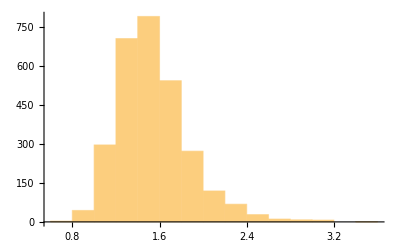

```mathematica
Histogram[data[[All,2,2]]]
```

```mathematica
{Mean[#],StandardDeviation[#]/√Length[#]}&@data[[All,2,2]]
```

{1.53845,0.00608386}

```mathematica
0.538 3.5
```

1.883

### Tension anisotropy (Fig. 5)

Tension anisotropy at individual vertices is calulated from the inferred tensions T_i at the vertex and the corresponding edge vectors in 3D space, e_i. The tensions T_i are normalized such that they sum to 1. We form the tensor 𝔗=∑_(i=1,2,3) T_i^2 e_i⊗e_i and calculate it’s eigenvalues and eigenvectors (in 3D space). The dominant eigenvector defines the local orientation of tension and is projected into the local tangent space for rendering in the pullbacks. One eigenvalue is zero, corresponding to the normal direction to the local tangent space. The magnitude of anisotropy is defined as the difference of the non-zero eigenvalues divided by their sum. 

After calculating tension anisotropy for each vertex we coarse-grain them on a spatial grid.

#### t=0 min (TP2)

```mathematica
vertexData=With[{t=2},With[{
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@Range[Length[vertexCoordsTS[[t]]]],
Length[#[[2]]]==3&]
},
(* Project shape director onto basis vectors *)
{toCylinder[#[[1]]],dirToTensor[#[[3,1]]{#[[2,1]].#[[3,3]],#[[2,2]].#[[3,3]]}]}&/@DeleteCases[
{vertexCoordsTS[[t,#[[1]]]],vertexLocalBasis[#[[1]],t],shapeMagPhaseDir[#[[2]]]}&/@verticesVecs,
{_,_,_Missing}
]
]
];//AbsoluteTiming
```

{6.90459,Null}

Binning grid size: 20x20 µm^2

```mathematica
binCounts=Length[#]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&];
```

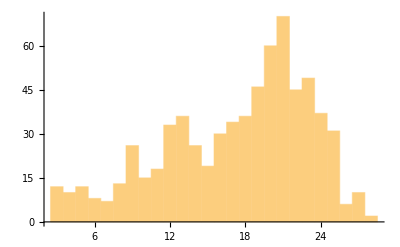

```mathematica
Histogram[binCounts]
```

```mathematica
N@Mean[binCounts]
```

17.2851

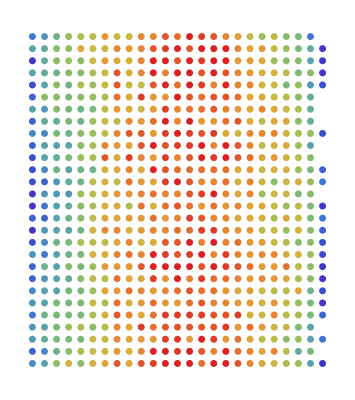

```mathematica
Graphics[{
AbsolutePointSize[5],
KeyValueMap[{ColorData["Rainbow"][#2/25],Point[#1]}&,binCounts]
}]
```

Near the anterior and posterior pole, fewer vertices are within each grid cell due to the map distortion. We are primarily interested in the central part of the embryo, where there are ca 20-25 vertices per grid cell.

```mathematica
binnedData=Mean[#[[All,2]]]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&];
```

```mathematica
headCells=Complement[Keys@Select[cellCentroidsTS[[1]],#[[1]]<150&],invaginatingCells,{3288}];
```

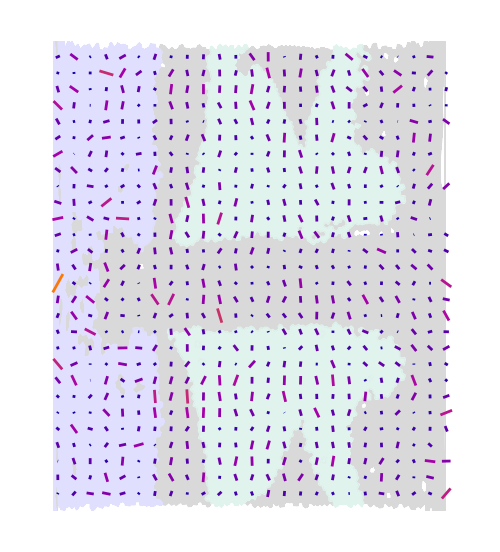

```mathematica
With[{t=2},Graphics[{
AbsolutePointSize[5],AbsoluteThickness[2],
FaceForm[LightGray],EdgeForm[LightGray],
renderCellGroup2D[invaginatingCells,t],
Through[Sequence[FaceForm,EdgeForm][zoneColorsLight[[1]]]],
renderCellGroup2D[headCells,t],
Through[Sequence[FaceForm,EdgeForm][zoneColorsLight[[2]]]],
renderCellGroup2D[bodyCells,t],
KeyValueMap[Function[{c,tensor},
With[{dir=tensorToDir[tensor]},{
Blend[{Darker@Blue,Darker@Magenta,Orange},1.5Norm[dir]],
Line[{c-20dir,c+20dir}]
}]],
binnedData
]},
ImageSize->500,Background->White,
PlotRange->{{5,510},{0,2π $radius}}
]
]
```

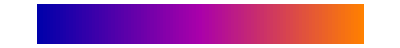

```mathematica
ArrayPlot[{Range[0,1,0.01]},ColorFunction->(Blend[{Darker@Blue,Darker@Magenta,Orange},#]&),AspectRatio->1/10,Frame->None,PlotRangePadding->None]
```

Distribution of tension anisotropy direction in the head vs the trunk (“body”)

```mathematica
bodyBins=Keys@Select[GroupBy[toCylinder/@Values[KeyTake[cellCentroidsTS[[2]],bodyCells]],{0,-10}+Round[{0,10}+#,20]&],Length[#]>2&];
headBins=Keys@Select[GroupBy[toCylinder/@Values[KeyTake[cellCentroidsTS[[2]],headCells]],{0,-10}+Round[{0,10}+#,20]&],Length[#]>2&];
```

```mathematica
renderRadialHistogram[data_,bspec_,hspec_]:=Module[{
histogramData=HistogramList[data,bspec,hspec]
},
{
Disk[{0,0},√(#[[1,2]]),{#[[1,1]],#[[2,1]]}]&/@Transpose[{
Transpose[{Most[histogramData[[1]]],histogramData[[2]]}],
Transpose[{Rest[histogramData[[1]]],histogramData[[2]]}]
}],
Disk[{0,0},√(#[[1,2]]),π+{#[[1,1]],#[[2,1]]}]&/@Transpose[{
Transpose[{Most[histogramData[[1]]],histogramData[[2]]}],
Transpose[{Rest[histogramData[[1]]],histogramData[[2]]}]
}]
}
]
```

```mathematica
renderRadialGridLines[bspec_,{min_,max_,step_}]:={
Line[{{0,0},√max{Cos[#],Sin[#]}}]&/@(Range@@bspec),
Circle[{0,0},√#]&/@Range[min,max,step]
}
```

Radial histogram (Fig. 5D, t = 0 min)

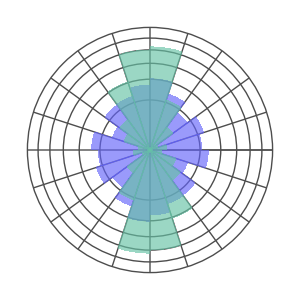

```mathematica
With[{
dataBody=WeightedData@@Transpose[({Mod[ArcTan@@#,π],Norm[#]}&@tensorToDir[#])&/@Values[KeyTake[binnedData,bodyBins]]],
dataHead=WeightedData@@Transpose[({Mod[ArcTan@@#,π],Norm[#]}&@tensorToDir[#])&/@Values[KeyTake[binnedData,headBins]]]
},
Graphics[{
GrayLevel[0.3],AbsoluteThickness[1],
renderRadialGridLines[{0,2π,π/10},{0.25,1.5,0.25}],
EdgeForm[None],
FaceForm[{Opacity[0.65],zoneColors[[1]]}],
renderRadialHistogram[dataHead,{0,π,π/10},"PDF"],
FaceForm[{Opacity[0.65],zoneColors[[2]]}],
renderRadialHistogram[dataBody,{0,π,π/10},"PDF"]
},
ImageSize->300,
Background->White
]
]
```

#### t=25 min (TP100); Fig. 5B

```mathematica
vertexData=With[{t=100},With[{
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@Range[Length[vertexCoordsTS[[t]]]],
Length[#[[2]]]==3&]
},
(* Project shape director onto basis vectors *)
{toCylinder[#[[1]]],dirToTensor[#[[3,1]]{#[[2,1]].#[[3,3]],#[[2,2]].#[[3,3]]}]}&/@DeleteCases[
{vertexCoordsTS[[t,#[[1]]]],vertexLocalBasis[#[[1]],t],shapeMagPhaseDir[#[[2]]]}&/@verticesVecs,
{_,_,_Missing}
]
]
];//AbsoluteTiming
```

{5.57521,Null}

```mathematica
binnedData=Mean[#[[All,2]]]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&];
```

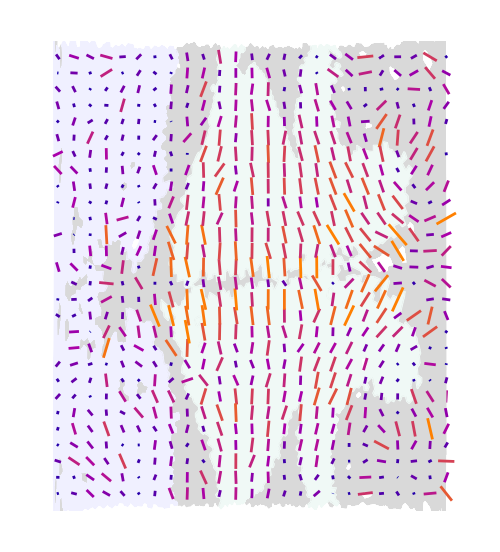

```mathematica
With[{t=100},Graphics[{
AbsolutePointSize[5],AbsoluteThickness[2],
FaceForm[LightGray],EdgeForm[LightGray],
renderCellGroup2D[invaginatingCells,t],
Through[Sequence[FaceForm,EdgeForm][zoneColorsLight[[1]]]],
renderCellGroup2D[headCells,t],
Through[Sequence[FaceForm,EdgeForm][zoneColorsLight[[2]]]],
renderCellGroup2D[bodyCells,t],
KeyValueMap[Function[{c,tensor},
With[{dir=tensorToDir[tensor]},{
Blend[{Darker@Blue,Darker@Magenta,Orange},1.5Norm[dir]],
Line[{c-20dir,c+20dir}]
}]],
binnedData
]},
ImageSize->500,Background->White,
PlotRange->{{5,510},{0,2π $radius}}
]
]
```

```mathematica
bodyBins=Keys@Select[GroupBy[toCylinder/@Values[KeyTake[cellCentroidsTS[[100]],bodyCells]],{0,-10}+Round[{0,10}+#,20]&],Length[#]>2&];
headBins=Keys@Select[GroupBy[toCylinder/@Values[KeyTake[cellCentroidsTS[[100]],headCells]],{0,-10}+Round[{0,10}+#,20]&],Length[#]>2&];
```

Radial histogram (Fig. 5D, t = 25 min)

```mathematica
With[{
dataBody=WeightedData@@Transpose[({Mod[ArcTan@@#,π],Norm[#]}&@tensorToDir[#])&/@Values[KeyTake[binnedData,bodyBins]]],
dataHead=WeightedData@@Transpose[({Mod[ArcTan@@#,π],Norm[#]}&@tensorToDir[#])&/@Values[KeyTake[binnedData,headBins]]]
},
Graphics[{
GrayLevel[0.3],AbsoluteThickness[1],
renderRadialGridLines[{0,2π,π/10},{0.25,1.5,0.25}],
EdgeForm[None],
FaceForm[{Opacity[0.65],zoneColors[[1]]}],
renderRadialHistogram[dataHead,{0,π,π/10},"PDF"],
FaceForm[{Opacity[0.65],zoneColors[[2]]}],
renderRadialHistogram[dataBody,{0,π,π/10},"PDF"]
},
ImageSize->300,
Background->White
]
]
```

-Graphics-

#### t=37 min (TP150)

```mathematica
vertexData=With[{t=150},With[{
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@Range[Length[vertexCoordsTS[[t]]]],
Length[#[[2]]]==3&]
},
(* Project shape director onto basis vectors *)
{toCylinder[#[[1]]],dirToTensor[#[[3,1]]{#[[2,1]].#[[3,3]],#[[2,2]].#[[3,3]]}]}&/@DeleteCases[
{vertexCoordsTS[[t,#[[1]]]],vertexLocalBasis[#[[1]],t],shapeMagPhaseDir[#[[2]]]}&/@verticesVecs,
{_,_,_Missing}
]
]
];//AbsoluteTiming
```

{4.17699,Null}

```mathematica
binnedData=Mean[#[[All,2]]]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&];
```

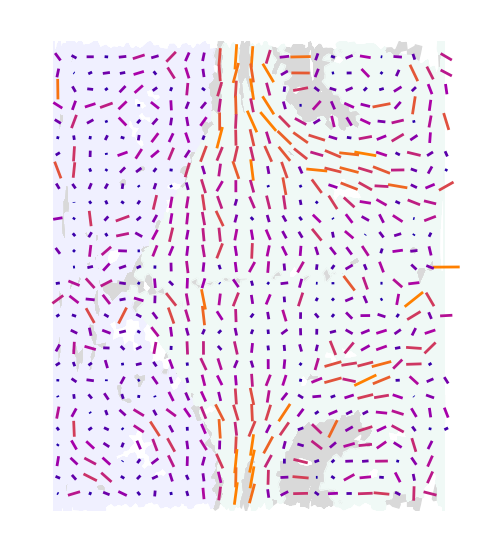

```mathematica
With[{t=150},Graphics[{
AbsolutePointSize[5],AbsoluteThickness[2],
FaceForm[LightGray],EdgeForm[LightGray],
renderCellGroup2D[invaginatingCells,t],
FaceForm[zoneColorsLight[[1]]],EdgeForm[zoneColorsLight[[1]]],
renderCellGroup2D[headCells,t],
FaceForm[zoneColorsLight[[2]]],EdgeForm[zoneColorsLight[[2]]],
renderCellGroup2D[bodyCells,t],
KeyValueMap[Function[{c,tensor},
With[{dir=tensorToDir[tensor]},{
Blend[{Darker@Blue,Darker@Magenta,Orange},1.5Norm[dir]],
Line[{c-20dir,c+20dir}]
}]],
binnedData
]},
ImageSize->500,Background->White,
PlotRange->{{5,510},{0,2π $radius}}
]
]
```

```mathematica
bodyBins=Keys@Select[GroupBy[toCylinder/@Values[KeyTake[cellCentroidsTS[[150]],bodyCells]],{0,-10}+Round[{0,10}+#,20]&],Length[#]>2&];
headBins=Keys@Select[GroupBy[toCylinder/@Values[KeyTake[cellCentroidsTS[[150]],headCells]],{0,-10}+Round[{0,10}+#,20]&],Length[#]>2&];
```

Radial histogram (Fig. 5D, t = 37 min)

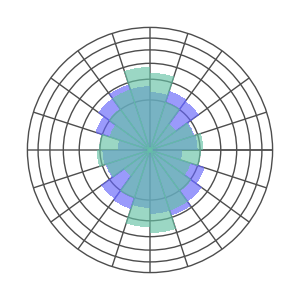

```mathematica
With[{
dataBody=WeightedData@@Transpose[({Mod[ArcTan@@#,π],Norm[#]}&@tensorToDir[#])&/@Values[KeyTake[binnedData,bodyBins]]],
dataHead=WeightedData@@Transpose[({Mod[ArcTan@@#,π],Norm[#]}&@tensorToDir[#])&/@Values[KeyTake[binnedData,headBins]]]
},
Graphics[{
GrayLevel[0.3],AbsoluteThickness[1],
renderRadialGridLines[{0,2π,π/10},{0.25,1.5,0.25}],
EdgeForm[None],
FaceForm[{Opacity[0.65],zoneColors[[1]]}],
renderRadialHistogram[dataHead,{0,π,π/10},"PDF"],
FaceForm[{Opacity[0.65],zoneColors[[2]]}],
renderRadialHistogram[dataBody,{0,π,π/10},"PDF"]
},
ImageSize->300,
Background->White
]
]
```

#### t=50min (TP198)

```mathematica
vertexData=With[{t=198},With[{
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@Range[Length[vertexCoordsTS[[t]]]],
Length[#[[2]]]==3&]
},
(* Project shape director onto basis vectors *)
{toCylinder[#[[1]]],dirToTensor[#[[3,1]]{#[[2,1]].#[[3,3]],#[[2,2]].#[[3,3]]}]}&/@DeleteCases[
{vertexCoordsTS[[t,#[[1]]]],vertexLocalBasis[#[[1]],t],shapeMagPhaseDir[#[[2]]]}&/@verticesVecs,
{_,_,_Missing}
]
]
];//AbsoluteTiming
```

{4.00069,Null}

```mathematica
binCounts=Length[#]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&];
```

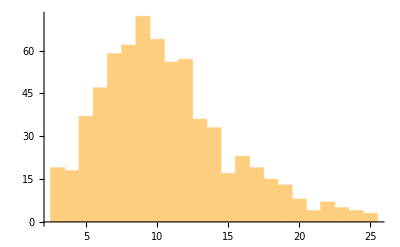

```mathematica
Histogram[binCounts]
```

```mathematica
binnedData=Mean[#[[All,2]]]&/@Select[GroupBy[vertexData,{0,-10}+Round[{0,10}+#[[1]],20]&],Length[#]>2&];
```

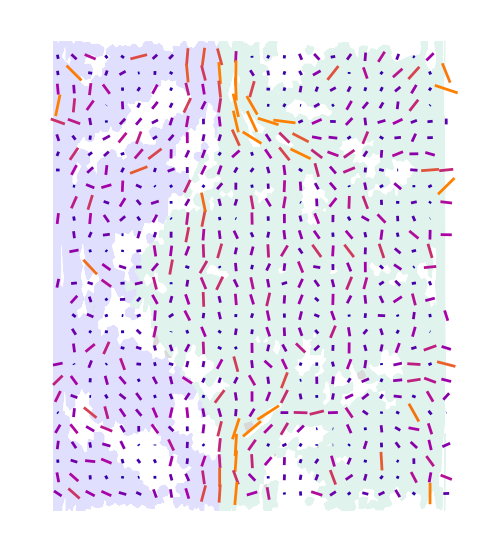

```mathematica
With[{t=198},Graphics[{
AbsolutePointSize[5],AbsoluteThickness[2],
FaceForm[LightGray],EdgeForm[LightGray],
renderCellGroup2D[invaginatingCells,t],
FaceForm[zoneColorsLight[[1]]],EdgeForm[zoneColorsLight[[1]]],
renderCellGroup2D[headCells,t],
FaceForm[zoneColorsLight[[2]]],EdgeForm[zoneColorsLight[[2]]],
renderCellGroup2D[bodyCells,t],
KeyValueMap[Function[{c,tensor},
With[{dir=tensorToDir[tensor]},{
Blend[{Darker@Blue,Darker@Magenta,Orange},1.5Norm[dir]],
Line[{c-20dir,c+20dir}]
}]],
binnedData
]},
ImageSize->500,Background->White,
PlotRange->{{5,510},{0,2π $radius}}
]
]
```

```mathematica
bodyBins=Keys@Select[GroupBy[toCylinder/@Values[KeyTake[cellCentroidsTS[[198]],bodyCells]],{0,-10}+Round[{0,10}+#,20]&],Length[#]>2&];
headBins=Keys@Select[GroupBy[toCylinder/@Values[KeyTake[cellCentroidsTS[[198]],headCells]],{0,-10}+Round[{0,10}+#,20]&],Length[#]>2&];
```

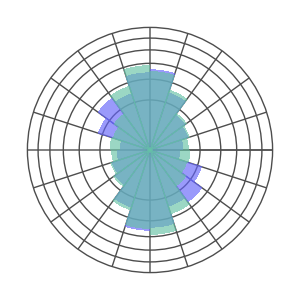

```mathematica
With[{
dataBody=WeightedData@@Transpose[({Mod[ArcTan@@#,π],Norm[#]}&@tensorToDir[#])&/@Values[KeyTake[binnedData,bodyBins]]],
dataHead=WeightedData@@Transpose[({Mod[ArcTan@@#,π],Norm[#]}&@tensorToDir[#])&/@Values[KeyTake[binnedData,headBins]]]
},
Graphics[{
GrayLevel[0.3],AbsoluteThickness[1],
renderRadialGridLines[{0,2π,π/10},{0.25,1.5,0.25}],
EdgeForm[None],
FaceForm[{Opacity[0.65],zoneColors[[1]]}],
renderRadialHistogram[dataHead,{0,π,π/10},"PDF"],
FaceForm[{Opacity[0.65],zoneColors[[2]]}],
renderRadialHistogram[dataBody,{0,π,π/10},"PDF"]
},
ImageSize->300,
Background->White
]
]
```

#### Small patches (individual vertices resolved)

```mathematica
inFrame[p_,{{x0_,x1_},{y0_,y1_}}]:=x0<p[[1]]<x1&&y0<p[[2]]<y1
```

```mathematica
renderROI[t_]:=Module[{roi={{220,270},{300,350}},cells,
vertices,verticesVecs,verticesData
},
cells=Keys[Select[
cellCentroidsTS[[t]],
inFrame[toCylinder[#],roi]&
]];
vertices=Union[Catenate[cellVerticesTS[[t]]/@cells]];
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@vertices,
Length[#[[2]]]==3&
];
verticesData={toCylinder[#[[1]]],#[[3,1]]{#[[2,1]].#[[3,3]],-#[[2,2]].#[[3,3]]}}&/@DeleteCases[
{vertexCoordsTS[[t,#[[1]]]],vertexLocalBasis[#[[1]],t],shapeMagPhaseDir[#[[2]]]}&/@verticesVecs,
{_,_,_Missing}
];
Graphics[{
FaceForm[None],EdgeForm[{Gray,AbsoluteThickness[1]}],
renderCell2D[#,t]&/@cells,
AbsoluteThickness[3],
{
Blend[{Darker@Blue,Darker@Magenta,Orange},Norm[#[[2]]]],
(*Blend[{Black,Red},1.2Norm[#[[2]]]],*)
Line[{#[[1]]-4#[[2]],#[[1]]+4#[[2]]}]
}&/@verticesData
},
PlotRange->roi,
Background->White,
ImageSize->200
]
]
```

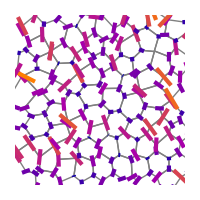
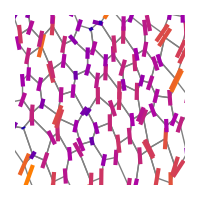
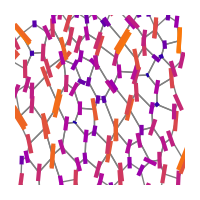
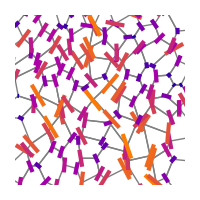
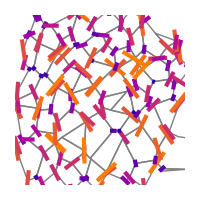

```mathematica
renderROI/@{1,80,100,150,198}
```

#### Tension anisotropy timetrace (Fig. 5C)

```mathematica
dataTS=Table[
With[{
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@DeleteMissing[Union[Flatten[cellVerticesTS[[t]]/@Catenate[dvStratifiedBodyCells[[1;;6]]]]]],
Length[#[[2]]]==3&]
},
(* Project shape director onto basis vectors *)
dirToTensor[#[[2,1]]{#[[1,1]].#[[2,3]],#[[1,2]].#[[2,3]]}]&/@DeleteCases[
{vertexLocalBasis[#[[1]],t],shapeMagPhaseDir[#[[2]]]}&/@verticesVecs,
{_,_Missing}
]
],
{t,1,198,5}
];//AbsoluteTiming
```

{97.4692,Null}

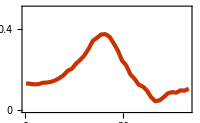

```mathematica
ListLinePlot[
Mean[#]&/@dataTS[[All,All,2,2]],
(*IntervalMarkers->"Bands",IntervalMarkersStyle->Directive["LineOpacity"->0],*)
PlotStyle->Thread[Directive[AbsoluteThickness[3],ColorData[112,1],{Default,Dashed}]],
PlotRange->{{0,50},{0,0.5}},
DataRange->{1,200}/4,
Frame->True,FrameStyle->Directive[16,Black],
FrameTicks->{{{0,0.2,0.4,0.6},None},{Range[0,50,10],None}},
(*FrameLabel->{"Time [min]","DV tension anisotropy"},*)
ImageSize->200,
PlotTheme->"PDFExport"
]
```

### Local tension configurations (LTC, tension triangle shape analysis)

#### LTC parameters from angles

Tension triangle vertices

```mathematica
T1={1,0};
T2=-{Cos[α],Sin[α]}Sin[β]/Sin[α+β];
T3=-T1-T2;
```

Barycentric coordinates

```mathematica
t1=T1-T2;
t2=-√3 T3;
```

Tangent of shape phase ψ

```mathematica
Simplify[2t1.t2/(t1.t1-t2.t2)]
```

(√3 Sin[α] Sin[α+2 β])/(Cos[2 α]-Cos[α] Cos[α+2 β])

```mathematica
shapePhase=ArcTan[(Cos[2 α]-Cos[α] Cos[α+2 β]),√3 Sin[α] Sin[α+2 β]];
```

Squared magnitude of anisotropy

```mathematica
shapeMagSq=FullSimplify[(4(t1.t2)^2+(t1.t1-t2.t2)^2)/(t1.t1+t2.t2)^2];
```

T1 threshold in LTC space

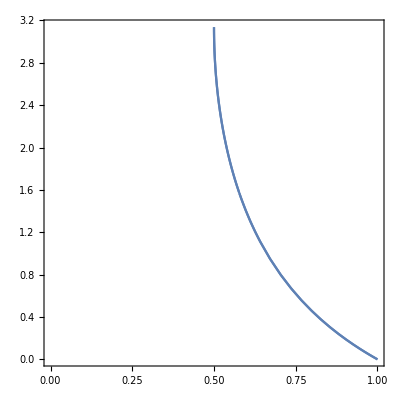

```mathematica
T1Threshold=ParametricPlot[Evaluate[{
√shapeMagSq,
Abs[Mod[3(π+Re@shapePhase),2π]-π](* map shape phase to the fundamental domain *)
}/.{β->π/2}(* In a symmetric kite, a T1 takes place when the angle opposite the shared edge is π/2 *)],
{α,0,π/2},
AspectRatio->1,
PlotRange->{{0,1},{0,π}},Frame->True
]
```

Triangle shape space

```mathematica
Manipulate[
With[{equiTri={{-1/2,-1/(2 √3)},{1/2,-1/(2 √3)},{0,1/(√3)}}},
With[{tri=(RotationMatrix[ϕ].{{((1-qψ[[1]])/(1+qψ[[1]]))^(1/4),0},{0,((1+qψ[[1]])/(1-qψ[[1]]))^(1/4)}}.RotationMatrix[qψ[[2]]/6].#)&/@equiTri},
Row[{
Show[Graphics[{},
PlotRange->{{0,1},{0,π}},AspectRatio->1,
Frame->True,FrameTicks->{{{0,{0.5π,"ψ",0},π},None},{{0,{0.5,"q",0},1},None}},FrameStyle->Directive[16,Black],
ImageSize->300
],
T1Threshold
],
Graphics[{
EdgeForm[{AbsoluteThickness[2],Black}],FaceForm[None],
Triangle[#-Mean[tri]&/@tri]
},
PlotRange->0.8Max[Table[Norm[tri[[Mod[i+1,3,1]]]-tri[[i]]],{i,3}]]{{-1,1},{-1,1}},
Frame->False,
ImageSize->300
]
},
Spacer[10]
]]
],
{{qψ,{0.5,0.5π}},Locator},{ϕ,0,π}
]
```

```mathematica
renderTriangle[{q_,ψ_},p_,s_]:=With[{equiTri={{-1/2,-1/(2 √3)},{1/2,-1/(2 √3)},{0,1/(√3)}}},
Triangle[((p+s RotationMatrix[π/2].{{((1-q)/(1+q))^(1/4),0},{0,((1+q)/(1-q))^(1/4)}}.RotationMatrix[ψ/6].#))&/@equiTri]
]
```

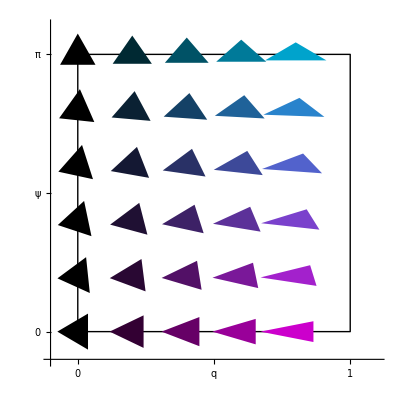

```mathematica
Graphics[{
EdgeForm[{Black,AbsoluteThickness[1]}],FaceForm[None],
Rectangle[{0,0},{1,1}],
EdgeForm[None],
Table[{
FaceForm[magentaCyanBlack[ψIter/π,qIter]],
renderTriangle[{qIter,ψIter},{qIter,ψIter/π},0.13]
},
{qIter,0,0.9,0.2},{ψIter,0,π,0.2π}
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Axes->True,AxesOrigin->{-0.1,-0.1},
Ticks->{{0,{0.5,"q",0},1},{0,{0.5,"ψ",0},{1,π}}},
AxesStyle->Directive[16,Black]
]
```

#### LTC Histograms (using non-smoothed edge vectors)

```mathematica
plotHistogram[data_,max_]:=Show[
Graphics[{Black,EdgeForm[None],Polygon[{{0,0},{0,π},{1,π},{1,0}}]},
AspectRatio->1,
PlotRange->{{-0.2,1.1},{-0.2π,1.1π}}
],
DensityHistogram[DeleteCases[data,{-1.0,0.0}|{_?(#>=1.0&),_}],{{0.1},{0.1π}},"PDF",
Method->{"DistributionAxes" -> "Histogram"},Background->White,
ColorFunction->(ColorData["SunsetColors"][#/max]&),
ColorFunctionScaling->False,
PerformanceGoal->"Speed" (* Turn of tooltips *)
]/.RGBColor[0.663226,0.6872815,0.911765]->GrayLevel[0.75],
Frame->True,FrameStyle->Directive[16,Black],
FrameTicks->{{{0,π},None},{{0,1},None}},
FrameLabel->{"Magnitude","Phase"},
ImageSize->Medium
]
```

0 min (before ventral furrow invagination)

We calculate the shape phase and magnitude of anisotropy from the edge vectors at a vertex using the function shapeMagPhase[] defined in setup.nb. Here’s the definition

```mathematica
?shapeMagPhase
```

```mathematica
data=With[{t=1},shapeMagPhase/@Select[
vertexVecs[#,t]&/@DeleteMissing[Union[Flatten[cellVerticesTS[[t]]/@bodyCells]]],
Length[#]==3&
]
];//AbsoluteTiming
```

{1.18549,Null}

```mathematica
plotHistogram[data,0.8]
```

-Graphics-

25 min (onset of GBE)

```mathematica
data=With[{t=25 4},shapeMagPhase/@Select[
vertexVecs[#,t]&/@DeleteMissing[Union[Flatten[cellVerticesTS[[t]]/@bodyCells]]],
Length[#]==3&
]
];//AbsoluteTiming
```

{1.26423,Null}

```mathematica
plotHistogram[data,0.8]
```

-Graphics-

45 min (near end of GBE)

```mathematica
data=With[{t=45 4},shapeMagPhase/@Select[
vertexVecs[#,t]&/@DeleteMissing[Union[Flatten[cellVerticesTS[[t]]/@bodyCells]]],
Length[#]==3&
]
];//AbsoluteTiming
```

{1.16504,Null}

```mathematica
plotHistogram[data,2]
```

-Graphics-

#### Timetrace of median shape phase and magnitude (using non-smoothed edge vectors); Fig. 8D

```mathematica
shapeStatsNonSmoothedTS=Table[
DeleteCases[
shapeMagPhase/@Select[
vertexVecs[#,t]&/@DeleteMissing[Union[Flatten[cellVerticesTS[[t]]/@bodyCells]]],
Length[#]==3&
],
{-1.,0.}
],
{t,1,198,1}
];//AbsoluteTiming
```

{229.881,Null}

Magnitude

```mathematica
shapeStatsNonSmoothedTS=DeleteCases[#,{-1.,0.}]&/@shapeStatsNonSmoothedTS;
```

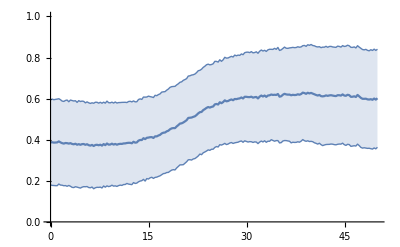

```mathematica
ListLinePlot[(Around[Median[#],StandardDeviation[#]]&@#[[All,1]])&/@shapeStatsNonSmoothedTS,
IntervalMarkers->"Bands",PlotRange->{0,1},DataRange->{0,50}
]
```

Phase (weighted by magnitude); Fig. 8D

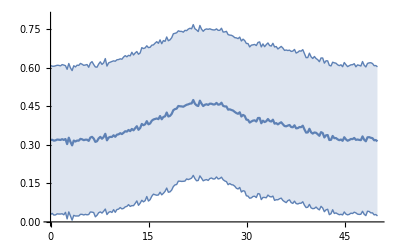

```mathematica
ListLinePlot[(1/π Around[Median[#],StandardDeviation[#]]&@WeightedData[#[[All,2]],#[[All,1]]])&/@shapeStatsNonSmoothedTS,
IntervalMarkers->"Bands",PlotRange->{0,0.8},DataRange->{0,50}
]
```

#### LTC Histograms (using smoothed edge vectors); Fig. 8C

To smooth out fluctuations, we want to average the orienations of edge vectors across subsequent timepoints. This requires that we have presistent identifiers for vertices. Each (non-degenarate) vertex is identified by three cells that it is part of. To track vertices, we therefore first generate a database of all cell triplets that ever exist (to save time, we only do it in the non-head, non-invaginating cells, short “body cells”), tagged with the timepoints at which they exist. From this data we can then extract the time intervals where each triplet exists.

```mathematica
bodyGraph=makeGraph[bodyCells,cellNeighborsTS[[1]]];
```

```mathematica
(* running this takes ca 10 min *)
allTripletsRaw=Monitor[Catenate@Table[
Thread[{t,Sort/@VertexList/@FindCycle[makeGraph[bodyCells,cellNeighborsTS[[t]]],{3},All]}],{t,Length[cellNeighborsTS]}
],t];//AbsoluteTiming
```

{606.242,Null}

```mathematica
checkForSurroundedCell[cycle_,t_]:=With[{
neighborhood=Union@@(getNeighborhood[#,t,1]&/@cycle)
},
Length@ConnectedComponents[VertexDelete[makeGraph[neighborhood,cellNeighborsTS[[t]]],cycle]]>1
]
```

```mathematica
(* running this takes ca 11 min *)
allTriplets=Select[allTripletsRaw,!checkForSurroundedCell[#[[2]],#[[1]]]&];//AbsoluteTiming
```

{709.647,Null}

```mathematica
tripletExistsTimes=#[[All,1]]&/@GroupBy[allTriplets,Last];
```

```mathematica
tripletExistsIntervals=findContinuousIntervals/@tripletExistsTimes;
```

Find the three edges that meet at a vertex via pairs of cells in the triplet. This way, the edge ordering will be consistent across timepoints.

```mathematica
tripletVecs[triplet_,t_]:=Module[{
cv=cellVerticesTS[[t]]/@triplet,
edges,
v0,x0,xi,
normalVec
},
(*If[Count[cv,_Missing]!=0,Return[SelectFirst[cv,MissingQ]]];*)
edges=Intersection@@#&/@Transpose[{cv,RotateLeft[cv]}];
(*If[Length[edges]==0,Return[$Failed]];*)
v0=(*If[Length[#]==0,Return[$Failed],First[#]]&@*)First@(Intersection@@edges);
x0=vertexCoordsTS[[t,v0]];
xi=vertexCoordsTS[[t,First[DeleteCases[#,v0]]&/@edges]];
normalVec=findLocalBasis[Join[{x0},xi]][[3]];
(#-x0)-(#-x0).normalVec normalVec&/@xi
]
```

Select the triplets that exist for all timeoints in a given time interval and subset of cells

```mathematica
containsIntervalQ[intervals_,{a_,b_}]:=AnyTrue[intervals,#[[1]]<=a&&b<=#[[2]]&]
```

```mathematica
selectTriplets[cells_,{t0_,t1_}]:=With[{
vertices=Select[DeleteMissing[Union[Flatten[cellVerticesTS[[t0]]/@cells]]],Length[vertexNeighborsTS[[t0,#]]]==3&]
},
Select[vertexCellsTS[[t0,vertices]],(!MissingQ[#]&&containsIntervalQ[#,{t0,t1}])&@tripletExistsIntervals[#]&]
];
```

Now we have all the infrastrcture we need to average the edge vector orientations across short time intervals and calculate the LTC parameters from them.

0 min

```mathematica
data=With[{t=1},
shapeMagPhase[Normalize/@Mean[Table[tripletVecs[#,tIter],{tIter,t,t+2} (* average over 0.5 mins (three timepoints) *)]]]&/@selectTriplets[zoneCells[[2]],{t,t+5}(* include only vertices that exist for the next 1.25 mins *)]
];//AbsoluteTiming
```

{1.81633,Null}

```mathematica
plotHistogram[data,1.2]
```

-Graphics-

25 min

```mathematica
data=With[{t=25 4},
shapeMagPhase[Normalize/@Mean[Table[tripletVecs[#,tIter],{tIter,t,t+2} (* average over 0.5 mins (three timepoints) *)]]]&/@selectTriplets[zoneCells[[2]],{t,t+5}(* include only vertices that exist for the next 1.25 mins *)]
];//AbsoluteTiming
```

{1.73006,Null}

```mathematica
plotHistogram[data,1.2]
```

-Graphics-

Note that compared to the non-smoothed analysis, there are significantly fewer degenerate triangles (anisotropy 1, phase 0).

45 min

```mathematica
data=With[{t=45 4},
shapeMagPhase[Normalize/@Mean[Table[tripletVecs[#,tIter],{tIter,t,t+2} (* average over 0.5 mins (three timepoints) *)]]]&/@selectTriplets[zoneCells[[2]],{t,t+5}(* include only vertices that exist for the next 1.25 mins *)]
];//AbsoluteTiming
```

{1.5764,Null}

```mathematica
plotHistogram[data,1.2]
```

-Graphics-

#### Timetrace of median shape phase and magnitude (using smoothed edge vectors)

```mathematica
(* takes ca 8 min to run *)
shapeStatsTS=Table[
DeleteCases[shapeMagPhase[Normalize/@Mean[Table[tripletVecs[#,t],{t,t0,t0+5}]]]&/@selectTriplets[bodyCells,{t0,t0+5}],
{-1.,0.}(* Remove degenerate vertices *)
],
{t0,1,198-5,2}
];//AbsoluteTiming
```

{493.655,Null}

Magnitude

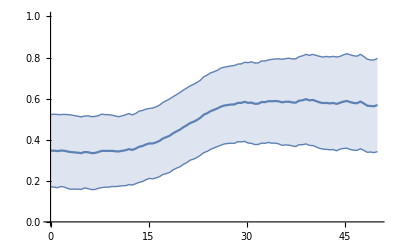

```mathematica
ListLinePlot[(Around[Median[#],StandardDeviation[#]]&@#[[All,1]])&/@shapeStatsTS,
IntervalMarkers->"Bands",PlotRange->{0,1},DataRange->{0,50}
]
```

Phase (weighted by magnitude)

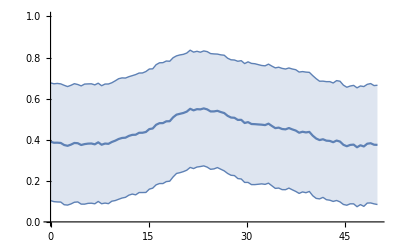

```mathematica
ListLinePlot[(1/π Around[Median[#],StandardDeviation[#]]&@WeightedData[#[[All,2]],#[[All,1]]])&/@shapeStatsTS,
IntervalMarkers->"Bands",PlotRange->{0,1},DataRange->{0,50}
]
```

#### LTC parameter rendering (Fig. 8S1)

```mathematica
renderFullFrame[t_]:=Module[{verticesVecs,verticesData},
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@Range[Length[vertexCoordsTS[[t]]]],
Length[#[[2]]]==3&
];
verticesData=DeleteCases[
{#[[1]],shapeMagPhase[#[[2]]]}&/@verticesVecs,
{_,_,_Missing}
];
Graphics[{
{
FaceForm[magentaCyanBlack[1-#[[2,2]]/π,#[[2,1]]]],EdgeForm[magentaCyanBlack[1-#[[2,2]]/π,#[[2,1]]]],
Polygon[toCylinder[cellCentroidsTS[[t]]/@vertexCellsTS[[t,#[[1]]]]]]
}&/@verticesData,
EdgeForm[White],FaceForm[None],
(*Rectangle[{220,300},{270,350}]*)
},
PlotRange->{{5,510},{-10,560}},
Background->Black,
ImageSize->600
]]
```

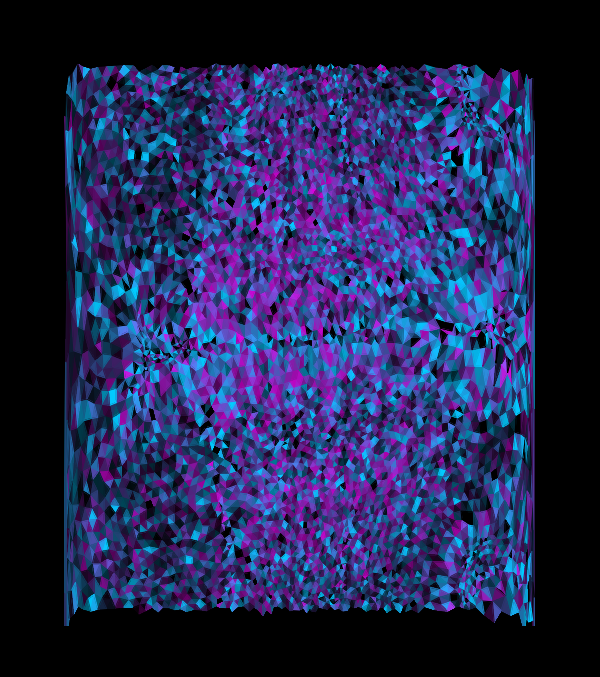

```mathematica
renderFullFrame[101]
```

Local patch

```mathematica
renderROI[t_]:=Module[{roi={{220,270},{300,350}},cells,
vertices,verticesVecs,verticesData
},
cells=Keys[Select[
cellCentroidsTS[[t]],
inFrame[toCylinder[#],roi]&
]];
vertices=Union[Catenate[cellVerticesTS[[t]]/@cells]];
verticesVecs=Select[
{#,vertexVecs[#,t]}&/@vertices,
Length[#[[2]]]==3&
];
verticesData=DeleteCases[
{#[[1]],shapeMagPhase[#[[2]]]}&/@verticesVecs,
{_,_,_Missing}
];
Graphics[{
{
FaceForm[magentaCyanBlack[1-#[[2,2]]/π,#[[2,1]]]],EdgeForm[magentaCyanBlack[1-#[[2,2]]/π,#[[2,1]]]],
Polygon[toCylinder[cellCentroidsTS[[t]]/@vertexCellsTS[[t,#[[1]]]]]]
}&/@verticesData,
FaceForm[None],EdgeForm[{Opacity[0.5],White,AbsoluteThickness[1.5]}],
renderCell2D[#,t]&/@cells
},
PlotRange->roi,
Background->Black,
ImageSize->200
]
]
```

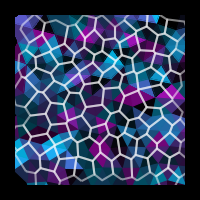
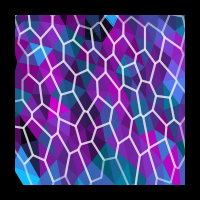
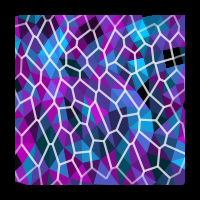
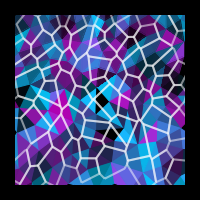
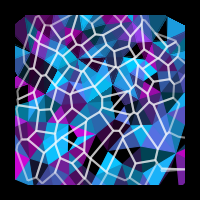

```mathematica
renderROI/@{2,80,120,150,198}
```